```mathematica
step=0.002;
z[x_,y_]:=x+I y;
f[x_]:= Exp [I x];
df[x_]:=f'[x];
g[z_]:=1/(z-0.5);
intf[end_]:=NIntegrate[g[f[x]] df[x],{x,0,end},MaxRecursion->1,AccuracyGoal->1]/Pi;
intfPlot=Accumulate[Table[g[f[x]] (f[x]-f[x-step]),{x,0,2 Pi,step}]];
```

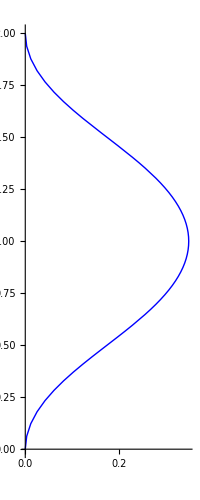

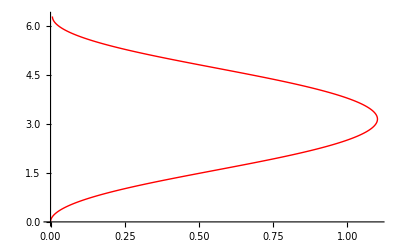

```mathematica
ParametricPlot[{Re[intf[x]],Im[intf[x]]},{x,0,2Pi},PlotStyle->{Blue},PlotPoints->2]
ListLinePlot[Transpose[{Re[intfPlot],Im[intfPlot]}],PlotStyle->{Red}]
```